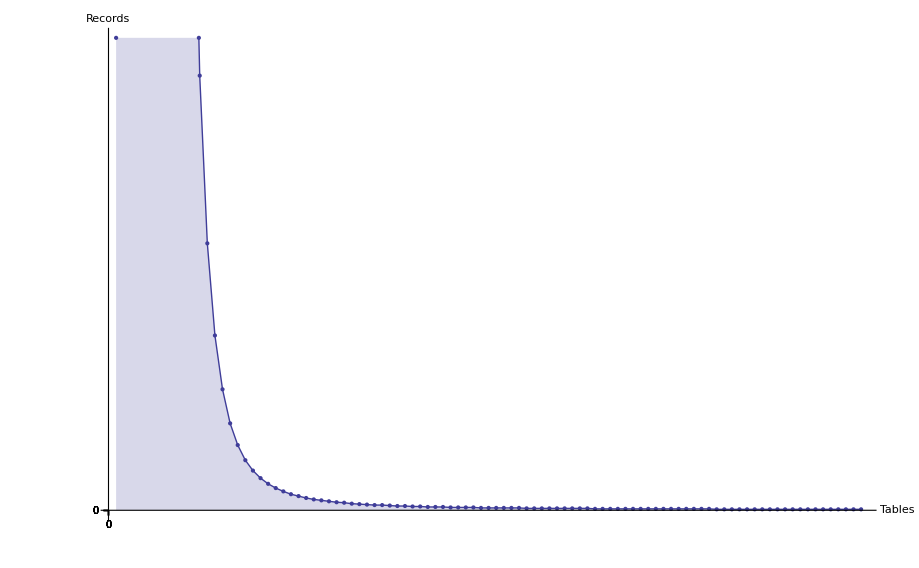

```mathematica
L = List[];
TicksT = List[];
TicksQ = List[];
GLT = List[];
GLQ = List[];
For[t =1, t < 10^2, t++,
a = Floor[Max[q/.FindInstance[∑_(i=0)^t (q^i (q - 1.))==2^128,q, Reals,t]]];
AppendTo[L, {t, a}];

AppendTo[TicksT, If[Mod[t, 2] == 0, t, 0]];
AppendTo[TicksQ, If[Mod[t, 2] == 0, a, 0]];
AppendTo[GLT, If[Mod[t, 2] == 0, {t, Dotted}, 0]];
AppendTo[GLQ, If[Mod[t, 2] == 0, {a, Dotted}, 0]];
];
ListLinePlot[L,Filling->Axis,DataRange->{0,100},PlotRange->{0,1000}, Mesh-> All, Ticks-> {TicksT, TicksQ},GridLines->{GLT, GLQ},AxesLabel->{"Tables", "Records"}]
```